```mathematica
xc=290;yc=80;
```

```mathematica
data={{xc,yc},
{xc-60,yc-60},
{xc-60-80,yc-60},
{xc-60-80-80,yc-60+80},
{xc-60-80-80,yc-60+80+140},
{xc-60-80-80+220,yc-60+80+140+220},
{xc+60+80+80,yc-60+80+140},
{xc+60+80+80,yc-60+80},
{xc+60+80,yc-60},
{xc+60,yc-60}}
```

{{290,80},{230,20},{150,20},{70,100},{70,240},{290,460},{510,240},{510,100},{430,20},{350,20}}

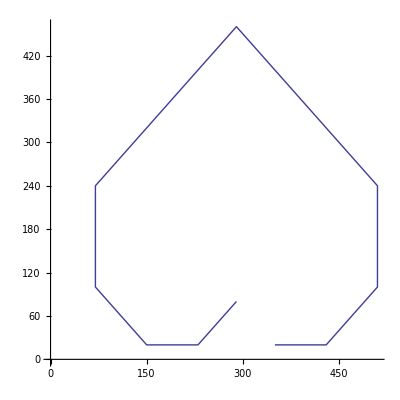

```mathematica
ListLinePlot[data,AspectRatio->1]
```